```mathematica
{{data = Import["E:\\Alessio\\Desktop\\Computazionale\\es11\\data.txt","Table"]}, {}};
```

```mathematica
M1 = Transpose[Take[data][[All, {2}]]];
M2 = Transpose[Take[data][[All, {3}]]];
M3 = Transpose[Take[data][[All, {4}]]];
```

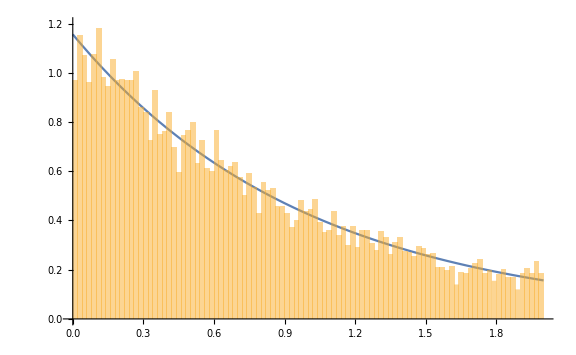

```mathematica
f1 = Exp[-x]/(1-Exp[-2]);
(*Integrate[f1, {x,0,2}]*)
Show[Plot[f1,{x,0,2}, PlotRange->{0,1.2}],Histogram[M1, 100,"PDF"]]
```

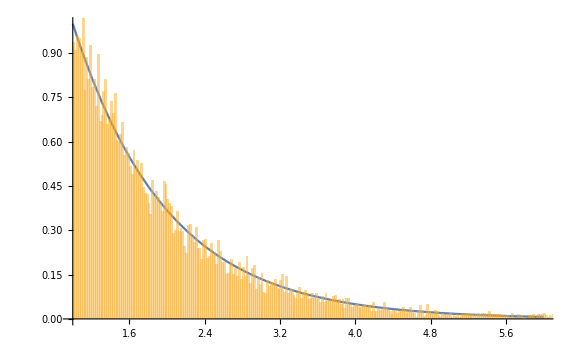

```mathematica
f2 = Exp[-x]/(1/ⅇ);
(*Integrate[f2,{x,1,Infinity}]*)
Show[Plot[f2,{x,1,6}],Histogram[M2,340,"PDF"]]
```

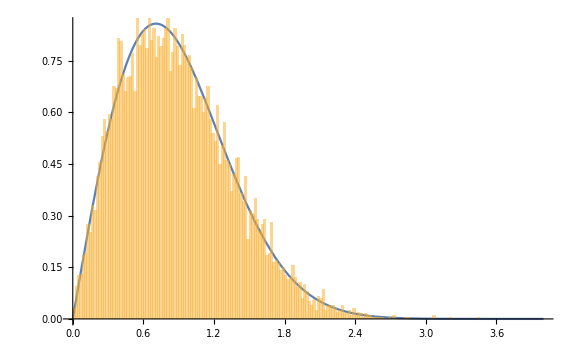

```mathematica
f3 = x*Exp[-x^2]/(1/2);
(*Integrate[f3,{x,0,Infinity}]*)
Show[Plot[f3,{x,0,4}],Histogram[M3, 100, "PDF"]]
```